```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

```mathematica
Simulación de retornos
```

de retornos Simulación

```mathematica
MeanReturns=Mean[database[[1]]["Returns"]];
stdReturns=StandardDeviation[database[[1]]["Returns"]];
database[[1]]["Returns"]//Histogram;
```

```mathematica
dias=1;
market=database[[1]];
intervaloDias=50;
randomV= RandomVariate[NormalDistribution[MeanReturns,stdReturns],Length[database[[1]]["Returns"]]];
retornoSimulados=randomV/Max[randomV];
Histogram[retornoSimulados];
```

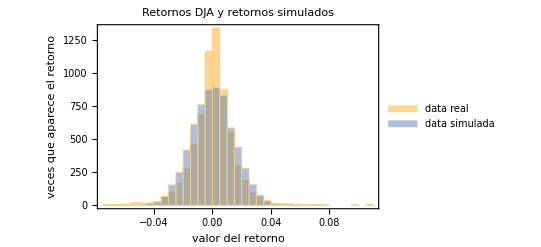

```mathematica
Histogram[{database[[1]]["Returns"],randomV},ChartLegends->{"data real", "data simulada"},PlotRange->Full,PlotLabel->"Retornos DJA y retornos simulados ", Frame->True,FrameLabel->{"valor del retorno","veces que aparece el retorno"},LabelStyle->Directive[Black,Bold]]
```

En el codigo de tesis final se estandarizan los retornos reales y los simulados, se hace lo mismo

### Primero para el mercado con valores reales.

```mathematica
returnRealEstandarizado=Standardize[database[[1]]["Returns"]];
```

### Ahora se estandarizan los valores de los retornos simulados

```mathematica
returnSimuladosEstandarizados=Standardize[randomV];
```

## Se dividen en cuartiles los retornos estandarizados de valores reales y de simulados

### Primero para el mercado con valores reales

```mathematica
Qreal=Quantile[returnRealEstandarizado,{1/4,1/2,3/4}];
```

### Ahora con el mercado cuyos retornos son simulados

```mathematica
Qsimula=Quantile[returnSimuladosEstandarizados,{1/4,1/2,3/4}];
```

## Se etiqueta cada intervalo con 1,2,3 o 4

### Se considera el dominio -∞ → ∞ en valores reales

```mathematica
intervaloReales=Partition[Join[{-∞},Qreal,{∞}],2,1]
```

{{-∞,-0.479041},{-0.479041,0.0393344},{0.0393344,0.513439},{0.513439,∞}}

### Se considera el dominio -∞ → ∞ en valores de retornos simulados

```mathematica
intervaloSimulados=Partition[Join[{-∞},Qsimula,{∞}],2,1]
```

{{-∞,-0.670403},{-0.670403,-0.00212579},{-0.00212579,0.658005},{0.658005,∞}}

Como son 4 elementos en la lista anterior, se ocupa Range[4] para las reglas de discretización

```mathematica
reglas[intervalo_]:=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalo,Range[4]}];
```

```mathematica
intervaloRDiscretizado=reglas[intervaloReales];
```

```mathematica
intervaloSDiscre=reglas[intervaloSimulados];
```

### Se aplican las reglas de discretización respectivas a cada retorno

#### A los retornos estandarizados de los precios reales

```mathematica
returnsDiscretosReales=returnRealEstandarizado/.intervaloRDiscretizado;
```

#### A los retornos simulados estandarizados

```mathematica
returnDiscretSimulados=returnSimuladosEstandarizados/.intervaloSDiscre;
```

### Se ordena retorno discretizado con su respectiva fecha, se toman las fecha reales para ordenar los datos {fecha,valor}

Primero para los datos reales

```mathematica
fechaReal=Drop[database[[1]]["Dates"],-1];
```

```mathematica
FechaRetornoReal=Transpose[{fechaReal,returnsDiscretosReales}];
```

Para los datos simulados

```mathematica
FechaRetornoSimulado=Transpose[{fechaReal,returnDiscretSimulados}];
```

## Ahora se procede a hacer el cálculo de la entropía

Con las siguientes dos funciones se facilita el cambiar la ventana de días que se quieren tomar en cuenta

```mathematica
particionRetReal[dias_]:=Partition[FechaRetornoReal,dias,1];
```

```mathematica
particionRetornoSimulados[dias_]:=Partition[FechaRetornoSimulado,dias,1];
```

### Esta es la entropia de los retornos reales

```mathematica
Sreal=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetReal[50]];
```

### A continuación, la entropía de los retornos simulados

```mathematica
SSimulada=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetornoSimulados[50]];
```

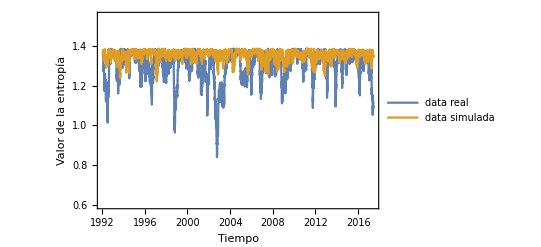

```mathematica
DateListPlot[{Sreal,SSimulada},PlotRange->{0.6,1.55},Frame->True,FrameLabel->{{"Valor de la entropía","2017"},{"Tiempo","Entropía de retornos reales y simulados"}},PlotLegends->{"data real", "data simulada"}]
```

```mathematica
Min[Sreal]
Max[Sreal]
```

```mathematica
Export["datareal.csv",Sreal]
```

```mathematica
Export["dataSSimulada.csv",SSimulada]
```

dataSSimulada.csv

## Ahora se obtienen los valores de entropía minima

```mathematica
Techo = N[Quantile[Map[N[Entropy[#[[All,2]]]]&,Particion],0.05]];
```

```mathematica
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
```

Part::partd: Part specification MAVReturns[<|Name→DJIA,Dates→{«1»},«6»,…→«1»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},{Day: ,0.00516862},«3269»,{Day: ,0.00588126},{Day: ,-0.010412}}|>,1]⟦«1»⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {MAVReturns[<|Name→DJIA,«8»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},{Day: ,0.00516862},«3269»,{Day: ,0.00588126},{Day: ,-0.010412}}|>,1]⟦All,1⟧,«18»} cannot be transposed.

Part::partd: Part specification MAVReturns[<|Name→DJIA,Dates→{«1»},«6»,…→«1»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},{Day: ,0.00516862},«3269»,{Day: ,0.00588126},{Day: ,-0.010412}}|>,1]⟦«1»⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {MAVReturns[<|Name→DJIA,«8»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},{Day: ,0.00516862},«3269»,{Day: ,0.00588126},{Day: ,-0.010412}}|>,1]⟦All,1⟧,Abs[«1»]+«1»} cannot be transposed.

DateDifference::date: Expression DateObject[{«1»,1,1}] cannot be interpreted as a date specification.

DateDifference::date: Expression MAVReturns[<|Name→DJIA,Dates→{«1»},«6»,…→«1»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},{Day: ,0.00516862},«3269»,{Day: ,0.00588126},{Day: ,-0.010412}}|>,1]⟦«1»⟧ cannot be interpreted as a date specification.

DateDifference::date: Expression DateObject[{«1»,1,1}] cannot be interpreted as a date specification.

General::stop: Further output of DateDifference::date will be suppressed during this calculation.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{«1»+QuantityMagnitude[DateDifference[DateObject[{«3»}],MAVReturns[«2»]⟦All,1⟧]]/(1.+MAVReturns[«2»]⟦All,1⟧[Year]),0.5 QuantityMagnitude[DateDifference[DateObject[{«3»}],MAVReturns[«2»]⟦All,1⟧]]+«1»,0.5 QuantityMagnitude[DateDifference[DateObject[{«3»}],MAVReturns[«2»]⟦All,1⟧]]+«1»},«1»} cannot be transposed.

$Aborted[]

DateDifference::date: Expression «1» cannot be interpreted as a date specification.

$Aborted[]

General::stop: Further output of DateDifference::date will be suppressed during this calculation.

```mathematica
DiscretizeByQuartiles[returns_]:=Block[{cuartailsStandardize,intervStandardize,discreStatesStandarizados,rulesStandarized},
cuartailsStandardize = Quantile[Standardize[returns],{1/4,1/2,3/4}];
intervStandardize = Partition[Join[{-∞},cuartailsStandardize,{∞}],2,1];
discreStatesStandarizados = Range[Length[intervStandardize]];
rulesStandarized = MapThread[x_/;IntervalMemberQ[Interval[#1],x]->#2&,{intervStandardize,discreStatesStandarizados}];

Standardize[returns]/. rulesStandarized
];
```

```mathematica
Quantile[Standardize[database[[1]]["Returns"]],{1/4,1/2,3/4}]
```

{-0.479041,0.0393344,0.513439}

```mathematica
Quantile[database[[1]]["Returns"],{1/4,1/2,3/4}]
```

{-0.00650255,0.000879896,0.00763187}